```mathematica
BunchWidth=200
Lifetime=166.5
BunchPeriod=1000
StartT=700
```

200

166.5

1000

700

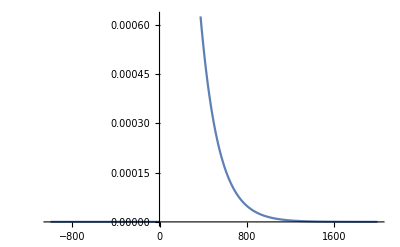

1.

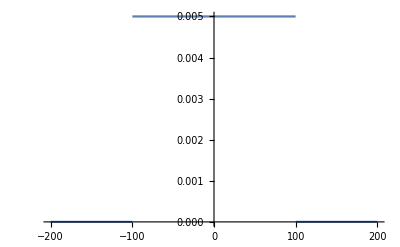

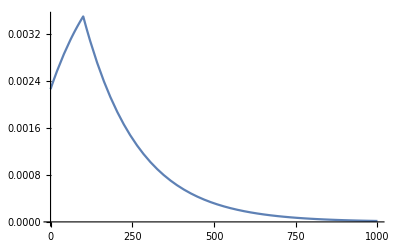

1.

0.013232

0.0132647

```mathematica
f[x_]:=1/Lifetime *Piecewise[ {{Exp[-x/Lifetime],x>0}},0] 
Plot[f[x],{x,-1000,2000}]
Integrate[f[x],{x,0,∞}]
g[y_]:=1/BunchWidth * Piecewise[{{1,-BunchWidth/2<y<BunchWidth/2}},0]
(*g[y_]:=PDF[NormalDistribution[0,50],y]*)
Plot[g[x],{x,-200,200}]
c[t_]:=Convolve[f[z],g[z],z,t]
Plot[c[x],{x,0,1000}]
Integrate[c[x],{x,-Infinity,Infinity}]
s[n_]:=NIntegrate[c[x],{x,StartT+BunchPeriod*n,BunchPeriod*(n+1)}]
NIntegrate[c[x],{x,StartT+BunchPeriod*0,BunchPeriod*1}]
Sum[s[n],{n,0,40}]
```